# FindRandomGridMazeSolution

Find a solution to a random grid maze

## Definition

```mathematica
PositiveIntegerQ//ClearAll
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
PositiveIntegerQ::usage="PositiveIntegerQ[n] returns True when n is a strictly positive integer.";
```

```mathematica
ClearAll[FindRandomGridMazeSolution]
```

```mathematica
FindRandomGridMazeSolution::usage="FindRandomGridMazeSolution[{m,n}] finds a solution and other data for a random grid maze of size m by n.";
```

```mathematica
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges. This is known as the trivial graph, the singleton, or the unit graph.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph,deadEnds,deadEndsCount,treeOutline},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->Iconize[shortestPath,"shortest-path"],"distance"->GraphDistance[m,start,end],"start"->start,"end"->end,"shortest-path-subgraph"->shortestPathSubgraph|>](*some ideas for other properties to add include deadends.*)
```

g::shdw: Symbol g appears in multiple contexts {PeterBurbery`BasicHypergeometricFunctions`Private`,Global`}; definitions in context PeterBurbery`BasicHypergeometricFunctions`Private` may shadow or be shadowed by other definitions.

v::shdw: Symbol v appears in multiple contexts {PeterBurbery`BasicHypergeometricFunctions`Private`,Global`}; definitions in context PeterBurbery`BasicHypergeometricFunctions`Private` may shadow or be shadowed by other definitions.

w::shdw: Symbol w appears in multiple contexts {PeterBurbery`BasicHypergeometricFunctions`Private`,Global`}; definitions in context PeterBurbery`BasicHypergeometricFunctions`Private` may shadow or be shadowed by other definitions.

w$::shdw: Symbol w$ appears in multiple contexts {PeterBurbery`BasicHypergeometricFunctions`Private`,Global`}; definitions in context PeterBurbery`BasicHypergeometricFunctions`Private` may shadow or be shadowed by other definitions.

## Documentation

### Usage

FindRandomGridMazeSolution[{m,n}]

finds a solution to a random maze of size m by n.

### Details & Options

How does this compare with https://resources.wolframcloud.com/FunctionRepository/resources/RandomMaze/ using the option "ShowSolution"-> True? 
Can you make an example comparing the two functions?
If the functionalities mainly overlap, we may reject this submission in favor of the existing resource function, unless you can show significant advantages in performance or functionality for your function.

The keys following the convention of alphanumeric characters lowercase separated by dash and hyphen, which is the convention for URLs and GitHub Repositories and which the ResourceFunction SlugifyString converts strings to.

This is from the documentation for FindShortestPath under Applications, third example where it states “Create a maze by random depth-first search of a grid graph:". I guess this functions depth-first search algorithm is faster than RandomMazes' breadth-first search algorithm. I didn't write the code for this function and I don't fully understand it, so I will give credit to the developers who built FindShortestPath.

I realize that some of my comments are specific to justifying this function and I don't want to be attacking or criticizing RandomMaze by making a straw man argument and comparing bad good to good code, but I put them to get the ResourceFunction published.

## Examples

### Basic Examples

Find a solution to a random 5 by 5 maze:

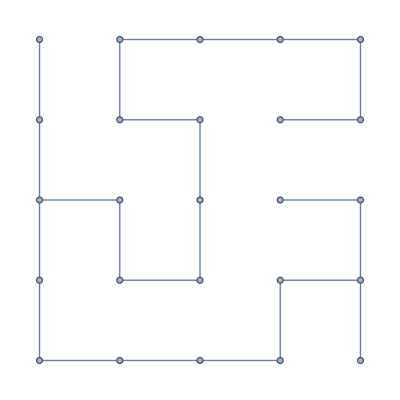
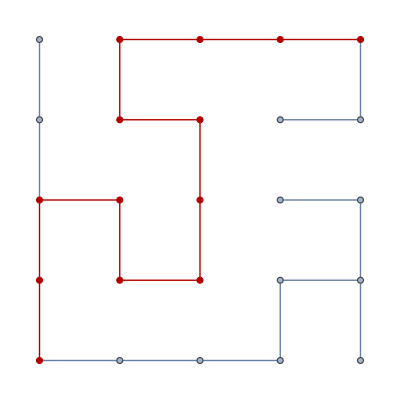
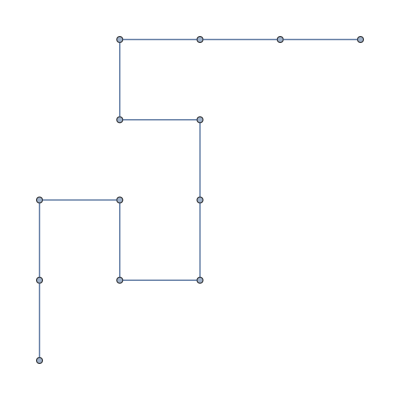
<|start→1,end→25,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→12,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{5,5}]
```

Find a solution to a random 10 by 10 maze:

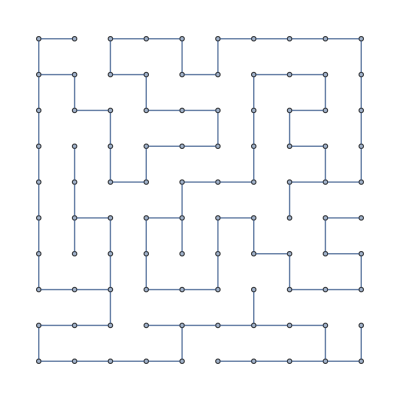
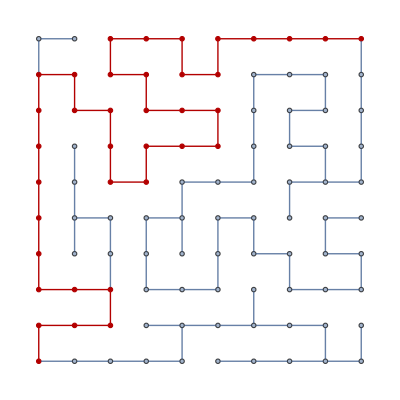
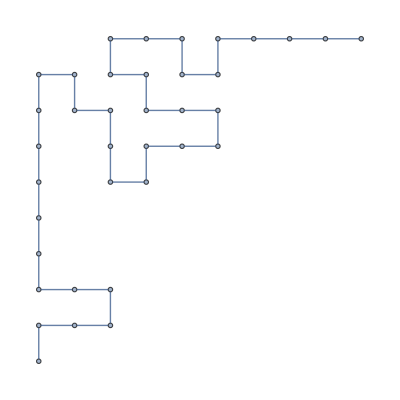
<|start→1,end→100,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→36,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{10,10}]
```

Find a solution to a random 15 by 15 maze:

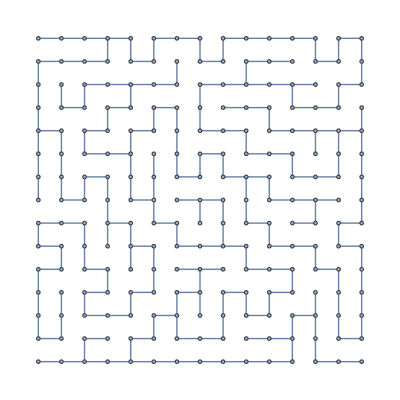
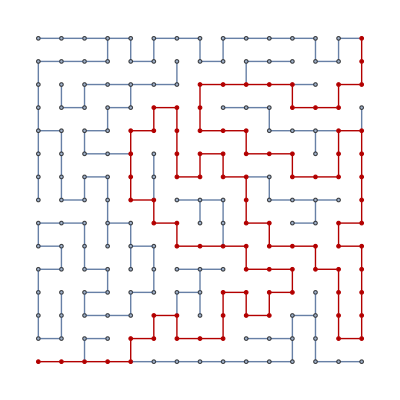
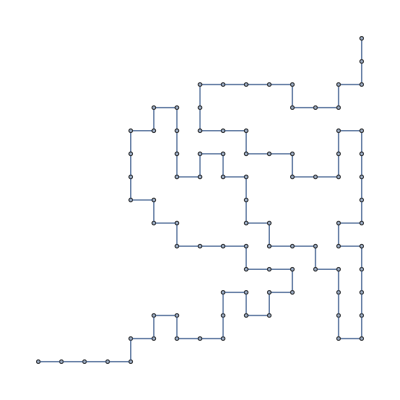
<|start→1,end→225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→90,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{15,15}]
```

### Scope

FindRandomGridMaze solution supports rectangular graphs where the height and width are different:

RandomMaze only supports square mazes.

A long short rectangular maze:

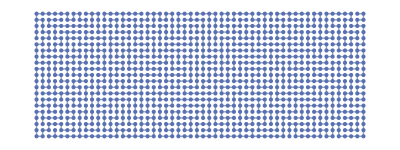
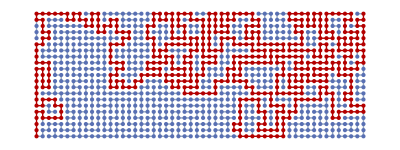
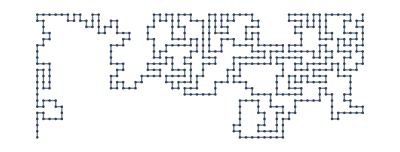
<|start→1,end→1134,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→501,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{21,54}]
```

A tall skinny narrow rectangular maze:

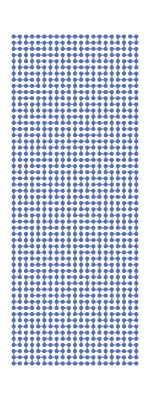
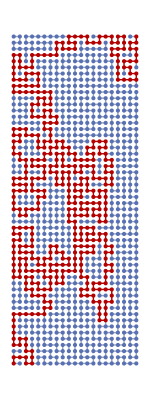
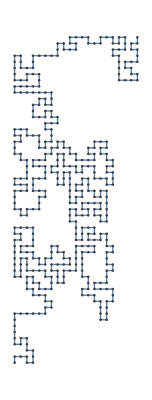
<|start→1,end→1134,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→431,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{54,21}]
```

The function supports small mazes. Make a random 7 by 7 maze:

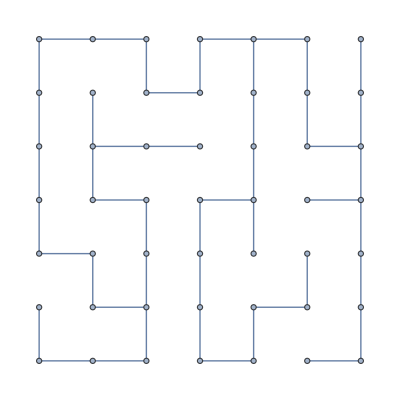
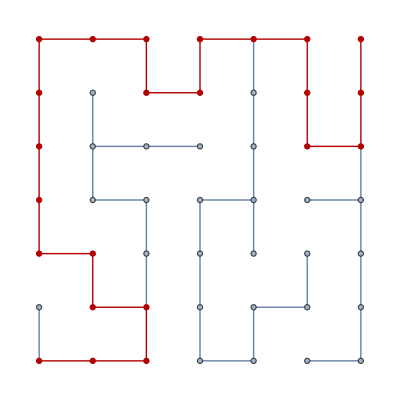
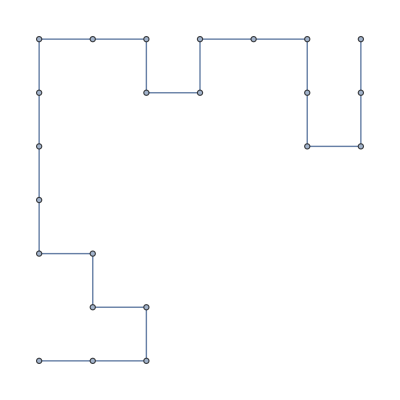
<|start→1,end→49,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→22,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{7,7}]
```

Make a random 10 by 10 maze:

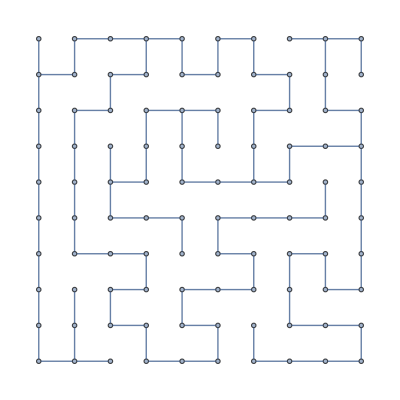
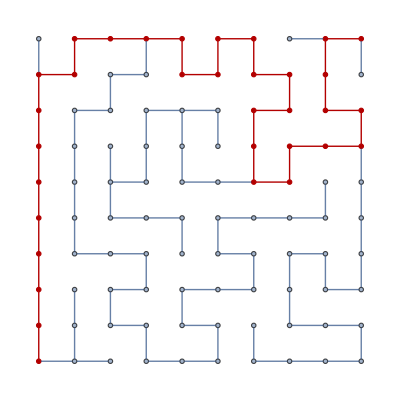
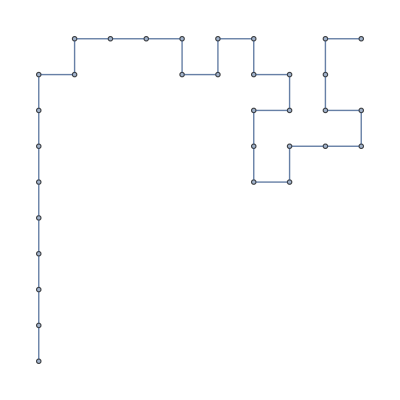
<|start→1,end→100,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→32,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{10,10}]
```

The function supports big mazes, too. Make a random 20 by 20 maze:

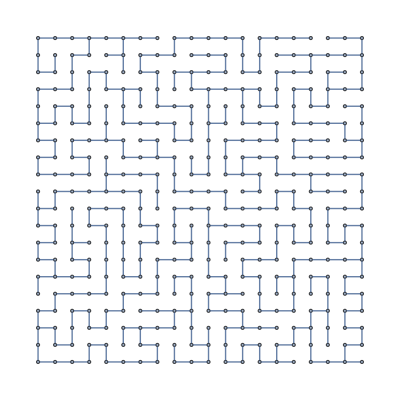
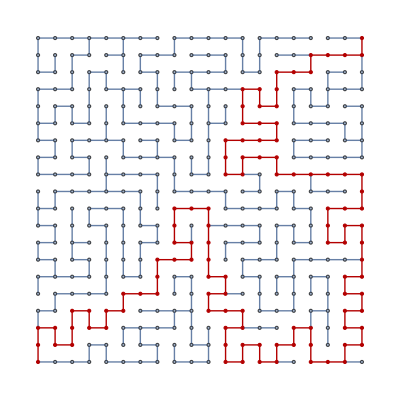
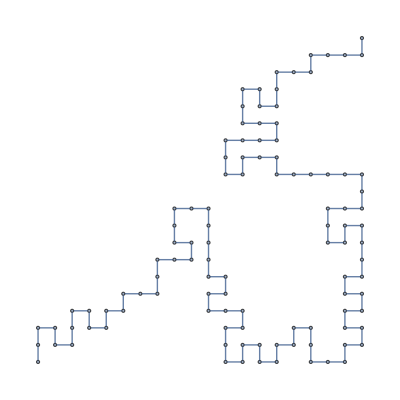
<|start→1,end→400,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→106,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{20,20}]
```

Make a random 25 by 25 maze:

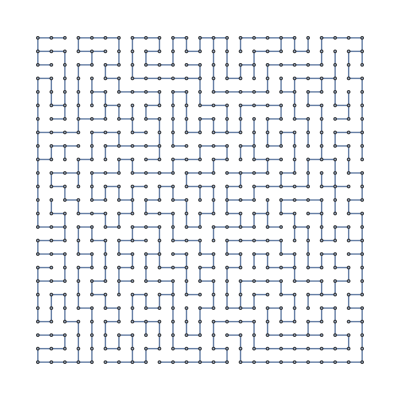
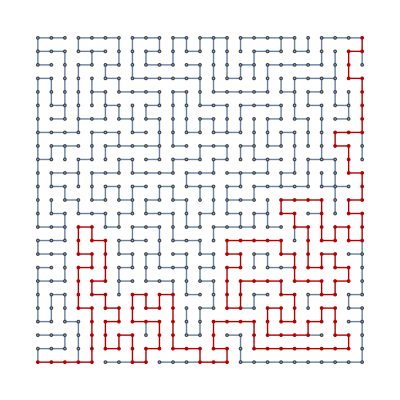
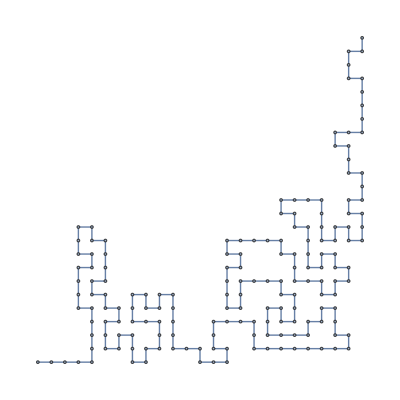
<|start→1,end→625,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→170,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{25,25}]
```

Make a random 30 by 30 maze:

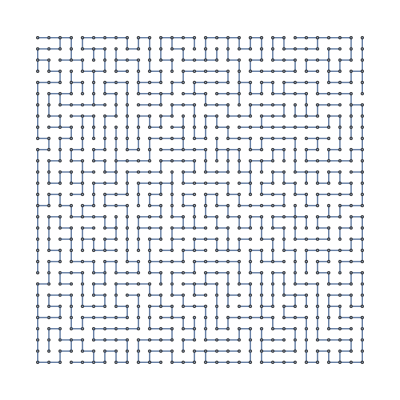
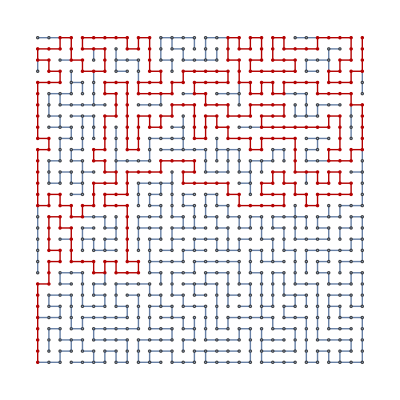
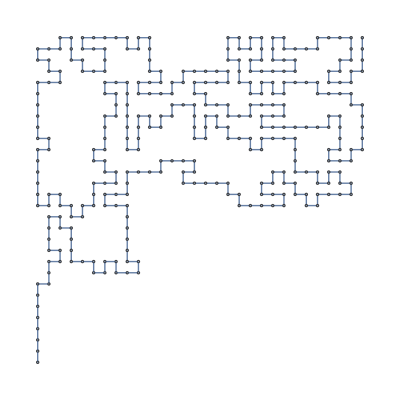
<|start→1,end→900,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→324,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{30,30}]
```

Make a random 35 by 35 maze:

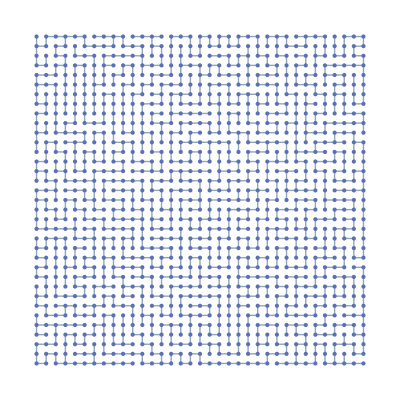
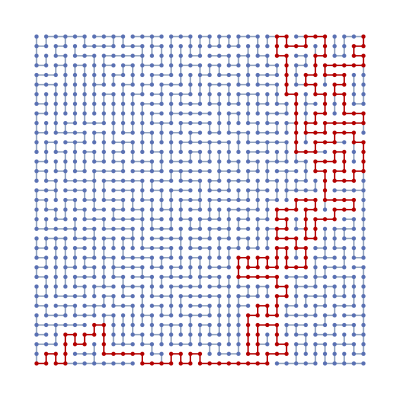
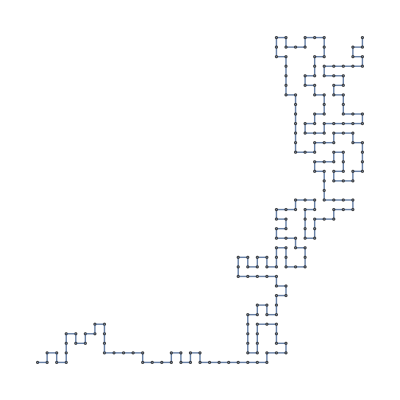
<|start→1,end→1225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→216,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{35,35}]
```

Make a random 40 by 40 maze and compute the timing:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{40,40}]]
```

0.1713

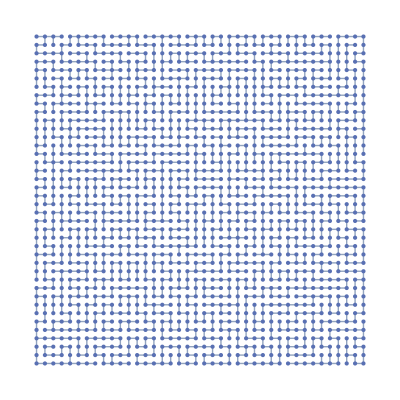
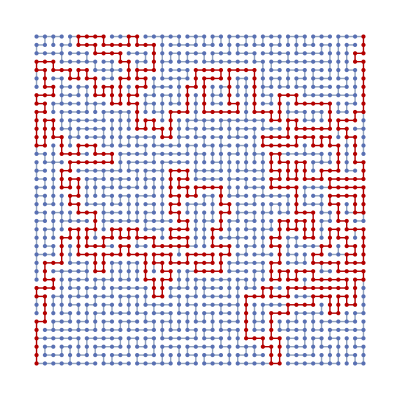
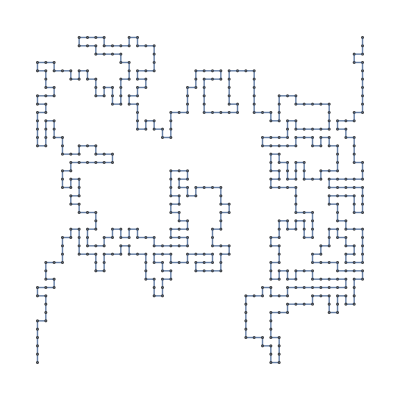
<|start→1,end→1600,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→548,shortest-path-subgraph→-Graphics-|>

Make a random 45 by 45 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{45,45}]]
```

0.232111

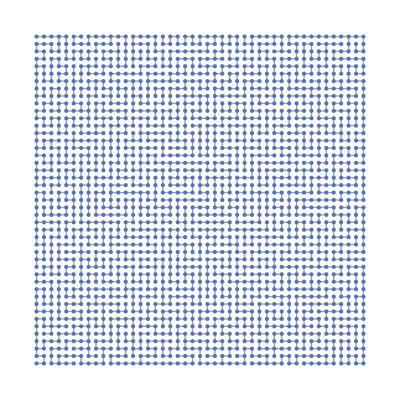
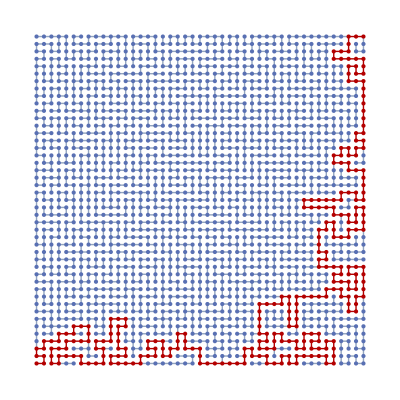
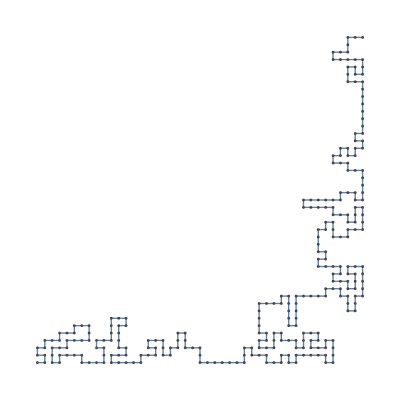
<|start→1,end→2025,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→278,shortest-path-subgraph→-Graphics-|>

Make a random 50 by 50 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{50,50}]]
```

0.299831

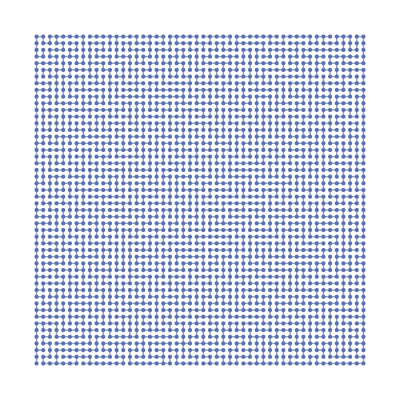
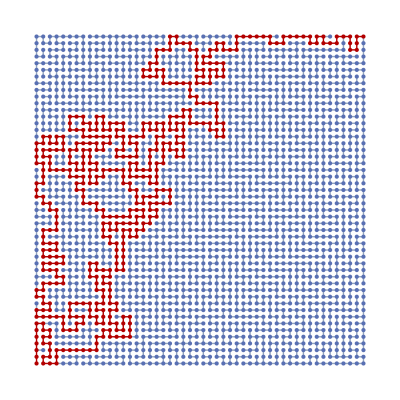
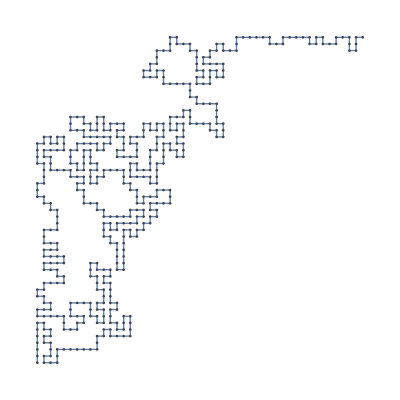
<|start→1,end→2500,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→484,shortest-path-subgraph→-Graphics-|>

Make a random 55 by 55 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{55,55}]]
```

0.433257

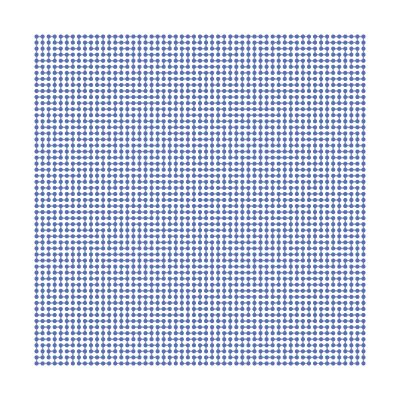
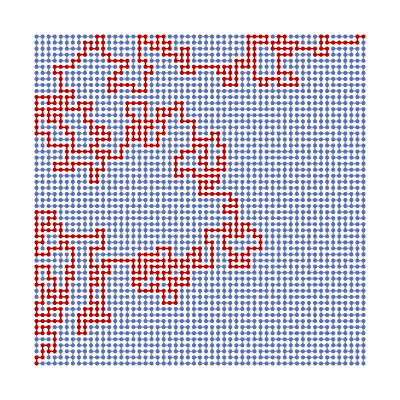
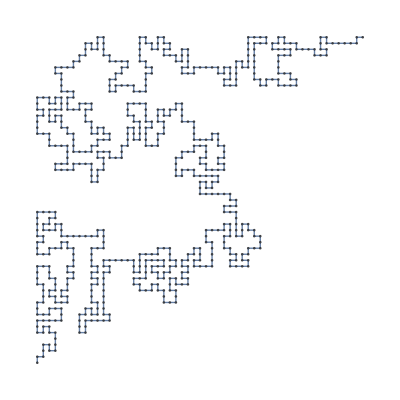
<|start→1,end→3025,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→672,shortest-path-subgraph→-Graphics-|>

Make a random 60 by 60 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{60,60}]]
```

0.539138

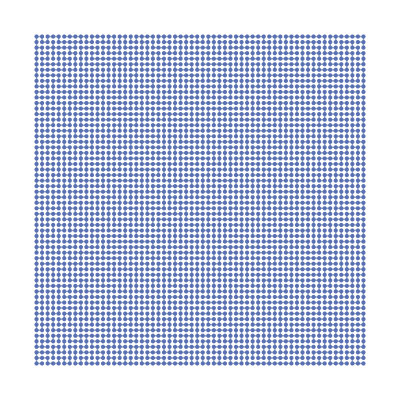
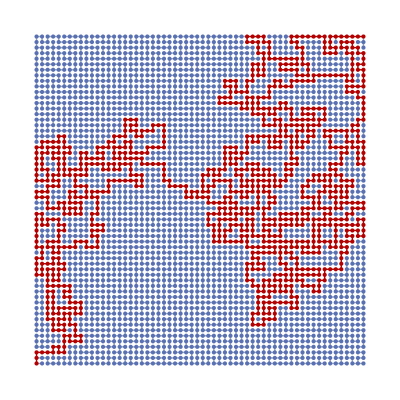
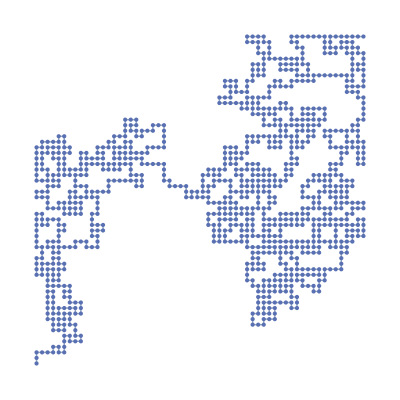
<|start→1,end→3600,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1060,shortest-path-subgraph→-Graphics-|>

Make a random 65 by 65 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{65,65}]]
```

0.70903

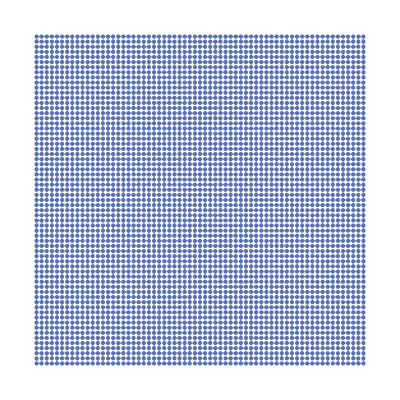
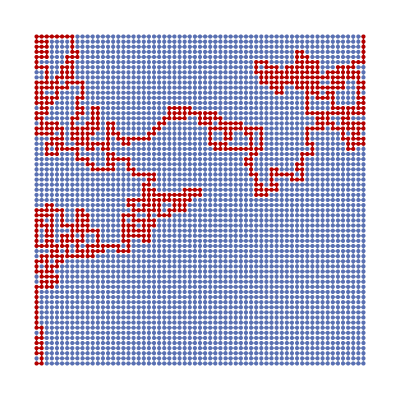
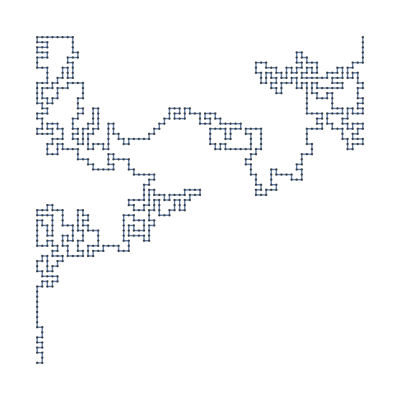
<|start→1,end→4225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→748,shortest-path-subgraph→-Graphics-|>

Make a random 70 by 70 maze. At this point, the maze and solved maze start getting hard to see, so the shortest-path subgraph is advantageous because its easier to see.:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{70,70}]]
```

0.841246

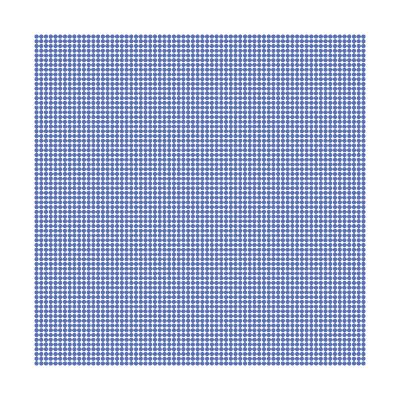
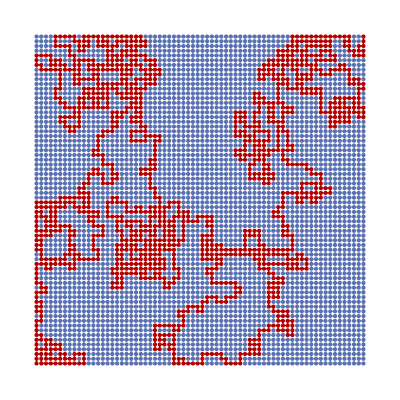
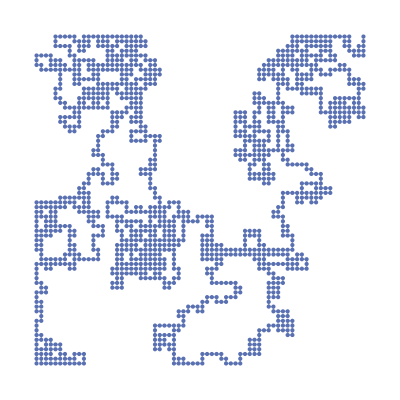
<|start→1,end→4900,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1430,shortest-path-subgraph→-Graphics-|>

Make a random 75 by 75 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{75,75}]]
```

1.10421

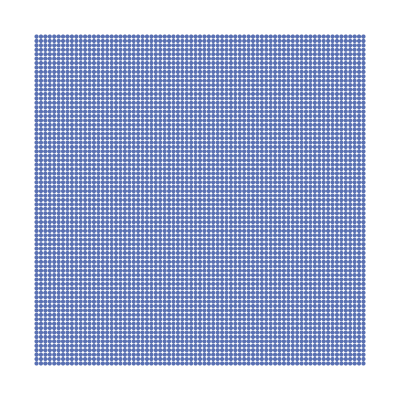
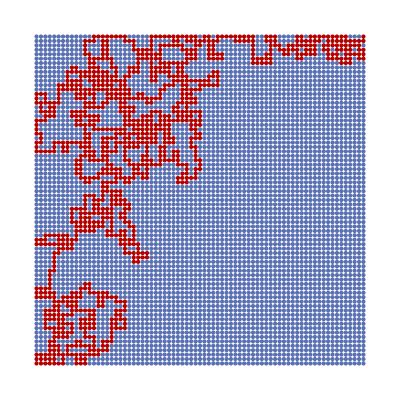
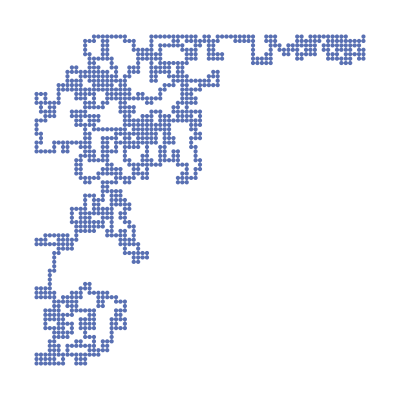
<|start→1,end→5625,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1134,shortest-path-subgraph→-Graphics-|>

Make a random 80 by 80 maze (at this point even the shortest-path subgraph is getting hard to understand):

```mathematica
EchoTiming[FindRandomGridMazeSolution[{80,80}]]
```

1.37651

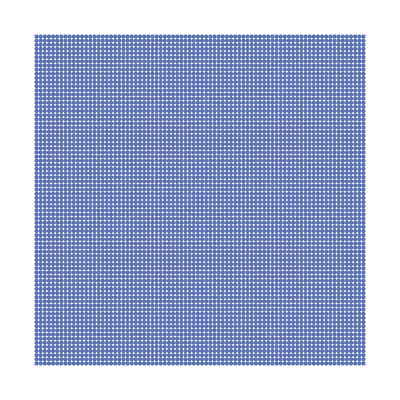
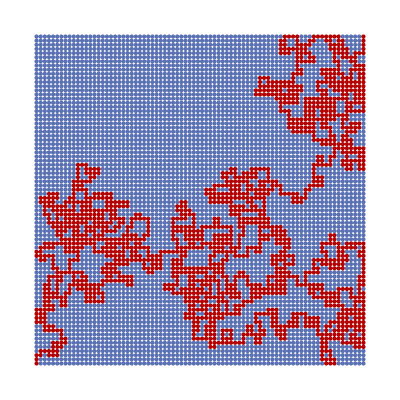
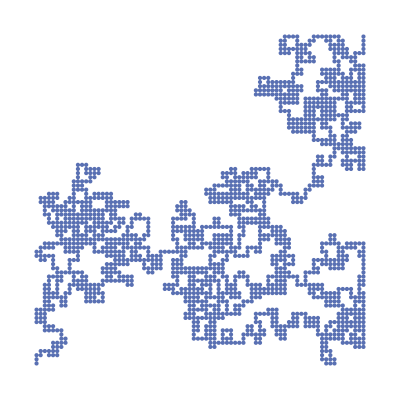
<|start→1,end→6400,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1782,shortest-path-subgraph→-Graphics-|>

Make a random 85 by 85 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{85,85}]]
```

1.64872

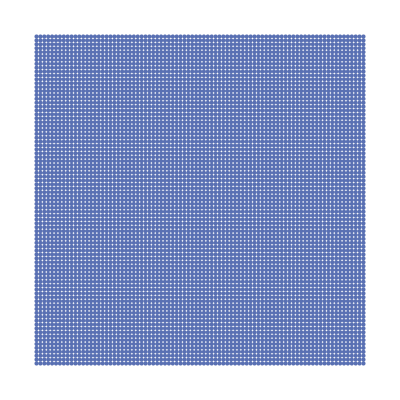
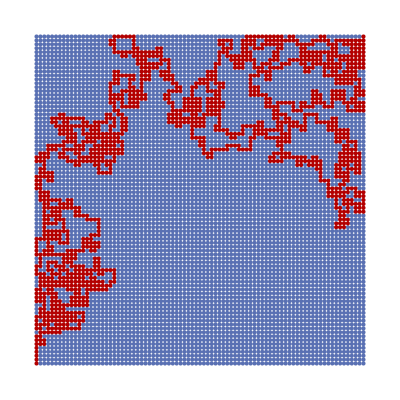
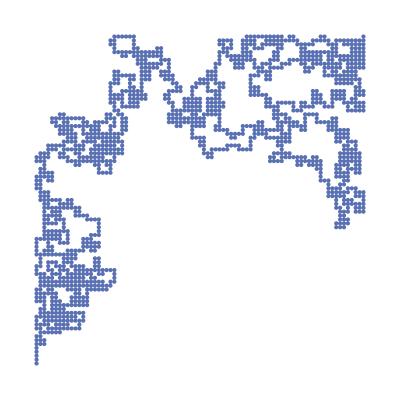
<|start→1,end→7225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1506,shortest-path-subgraph→-Graphics-|>

We are approaching the limit of this function. We cannot go past 100 by 100.

```mathematica
EchoTiming[FindRandomGridMazeSolution[{90,90}]]
```

1.96134

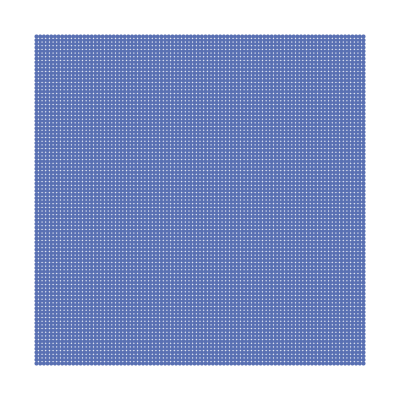
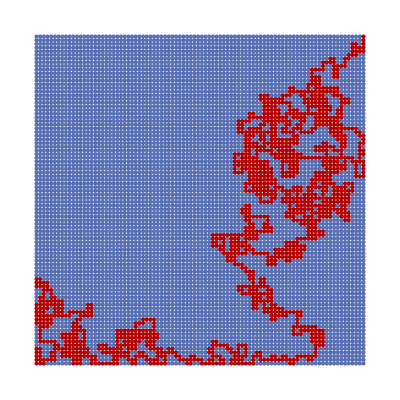
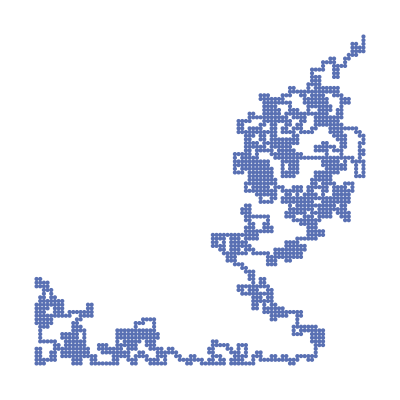
<|start→1,end→8100,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1458,shortest-path-subgraph→-Graphics-|>

Make a random 95 by 95 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{95,95}]]
```

2.40227

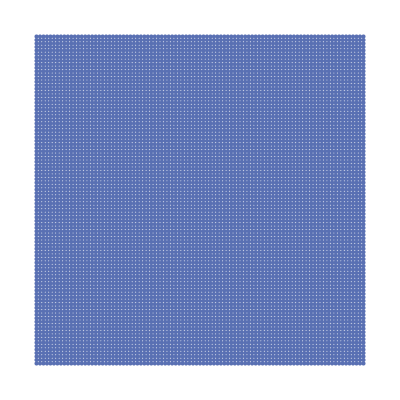
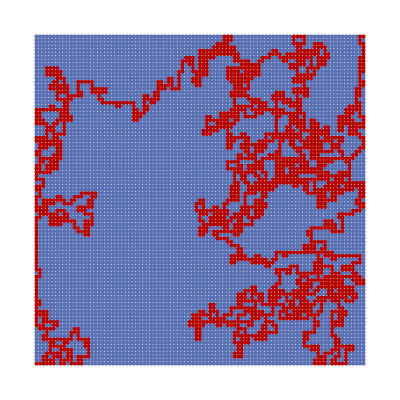
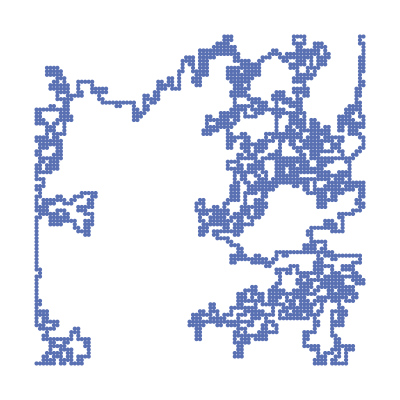
<|start→1,end→9025,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→2324,shortest-path-subgraph→-Graphics-|>

Make a random 100 by 100 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{100,100}]]
```

2.96479

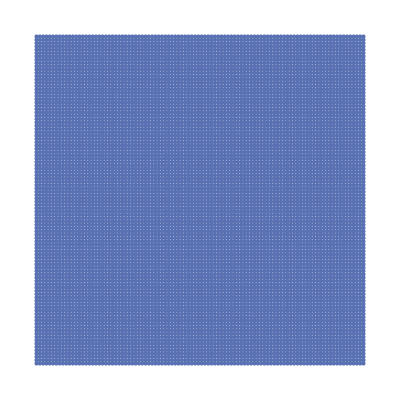
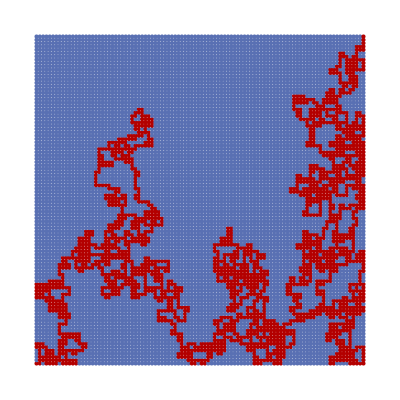
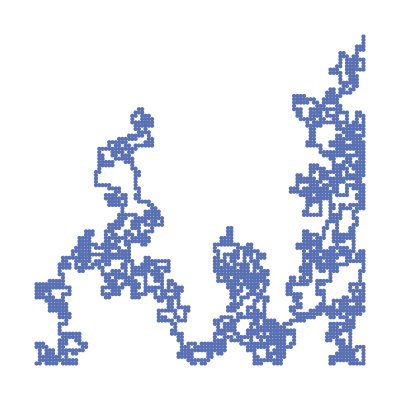
<|start→1,end→10000,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→2298,shortest-path-subgraph→-Graphics-|>

If we go up even by 1 to 101 by 101 the maze and solved-maze don't work.:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{101,101}]]
```

2.98184

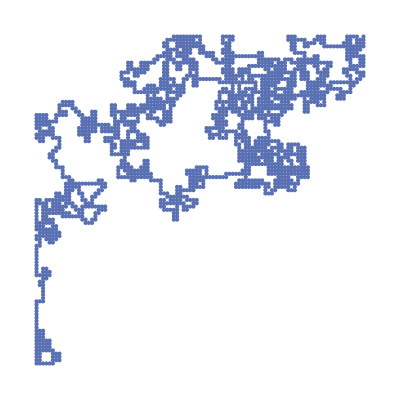
<|start→1,end→10201,maze→,solved-maze→,shortest-path→,distance→1896,shortest-path-subgraph→-Graphics-|>

The function returns a Graph, which can be used for further analysis.

### Properties & Relations

Compare the timing of FindRandomGridMazeSolution to RandomMaze:

```mathematica
EchoTiming@FindRandomGridMazeSolution[{100,100}]
```

2.93385

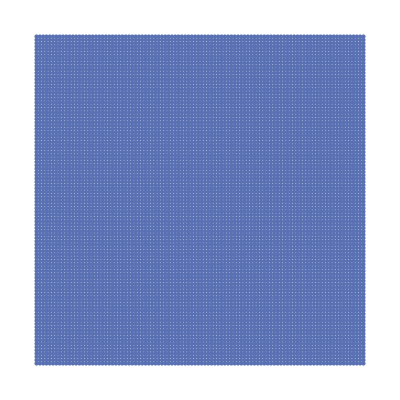
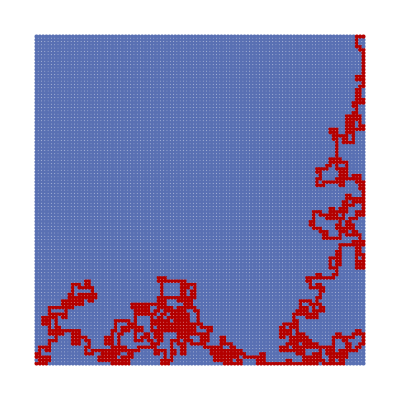
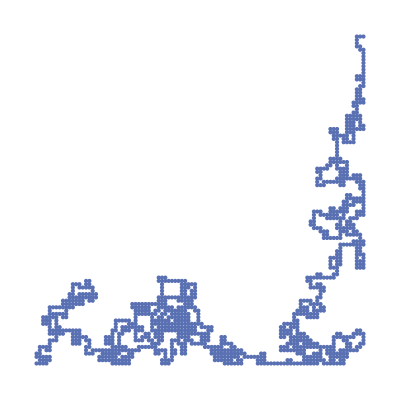
<|start→1,end→10000,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1146,shortest-path-subgraph→-Graphics-|>

```mathematica
First@RepeatedTiming@FindRandomGridMazeSolution[{100,100}]
```

2.94379

```mathematica
EchoTiming@ResourceFunction["RandomMaze"][100]
```

56.6464

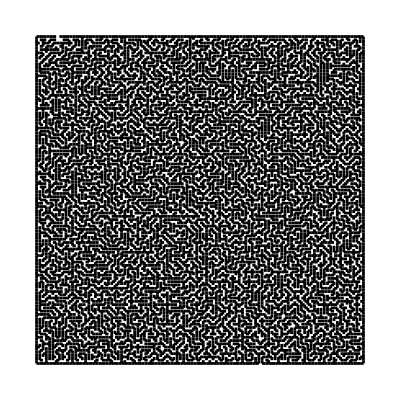

The function is about 19 times faster compared to RandomMaze:

```mathematica
56.6463813/2.9338526
```

19.3078

This function is much faster than RandomMaze for large inputs.

Here are some more timing tests. My approach will be to create a CloudExpression with CreateCloudExpression with an empty association <||> that I will put RepeatedTiming for mazes from 30 to 100 in increments of 10 for the ResourceFunction RandomMaze and my submission of FindRandomGridMazeSolution. I will then compare the total time it takes:

Create a cloud expression to store timing data for RandomMaze:

```mathematica
randomMazeTiming=CreateCloudExpression[<||>,"randomMazeTimingData"]
```

CloudExpression[…]

Store a value:

```mathematica
randomMazeTiming["30"]=First[Quiet[RepeatedTiming[ResourceFunction["RandomMaze"][30]],{First::nofirst,Part::take}]]
```

0.63955

Create a function to do iterate through the process of performing timing:

```mathematica
storeRandomMazeTimingFunction[x_?IntegerQ]:=randomMazeTiming[ToString[x]]=First[Quiet[RepeatedTiming[ResourceFunction["RandomMaze"][x]],{First::nofirst,Part::take}]]
```

Do the timing:

```mathematica
Do[storeRandomMazeTimingFunction[i],{i,30,100,10}]
```

Get the timing results:

```mathematica
Sort@Get[randomMazeTiming]
```

<|40→1.03409,30→2.18132,60→3.67364,50→13.8107,70→18.6532,80→40.6946,90→48.7303,100→197.233|>

```mathematica
Transpose[{ToExpression@Keys[#],Values[#]}&[Sort@Get[randomMazeTiming]]]
```

{{40,1.03409},{30,2.18132},{60,3.67364},{50,13.8107},{70,18.6532},{80,40.6946},{90,48.7303},{100,197.233}}

```mathematica
FullForm[%786]
```

List[List[40,1.03409],List[30,2.18132],List[60,3.67364],List[50,13.8107],List[70,18.6532],List[80,40.6946],List[90,48.7303],List[100,197.233]]

```mathematica
Dimensions[Transpose[{Keys[#],Values[#]}&[Sort@Get[randomMazeTiming]]]]
```

{8,2}

```mathematica
Depth[Transpose[{Keys[#],Values[#]}&[Sort@Get[randomMazeTiming]]]]
```

3

```mathematica
FindFormula[{{40,1.0340934},{30,2.1813152},{60,3.6736362},{50,13.8106594},{70,18.653185},{80,40.6945934},{90,48.7303379},{100,197.2329061}},x,15,All]
```

This is a cloud expression for FindRandomGridMazeSolution:

```mathematica
FindRandomGridMazeSolutionTiming=CreateCloudExpression[<||>,"FindRandomGridMazeSolutionTiming"]
```

CloudExpression[…]

This is a function to time how fast FindRandomGridMazeSolution is:

```mathematica
findRandomGridMazeSolutionTimingFunction[x_?IntegerQ]:=FindRandomGridMazeSolutionTiming[ToString[x]]=First[Quiet[RepeatedTiming[FindRandomGridMazeSolution[x]],{First::nofirst,Part::take}]]
```

Do the timing:

```mathematica
Do[findRandomGridMazeSolutionTimingFunction[i],{i,30,100,10}]
```

Get the timing results:

```mathematica
Get[FindRandomGridMazeSolutionTiming]
```

<|30→2.10024×10^-8,40→2.23814×10^-8,50→2.08957×10^-8,60→2.21422×10^-8,70→2.09859×10^-8,80→2.19656×10^-8,90→2.20077×10^-8,100→2.16435×10^-8|>

Put the timing results in a dataset:

```mathematica
data=Dataset[<|"RandomMaze"->Get@randomMazeTiming,"FindRandomGridMazeSolution"->Get@FindRandomGridMazeSolutionTiming|>]
```

Get totals for each row by applying Total to all columns for all the rows, then sort:

```mathematica
data[Sort,Total]
```

Sort, then use the ResourceFunction ReadableTimeString to convert raw seconds into a human-readable amount of time:

```mathematica
data[Sort,ResourceFunction["ReadableTimeString"][#,"PrefixShort"->False,"Decimals"->3]&@*Total]
```

Make a pie-chart (notice that FindRandomGridMazeSolution's times are consistent whereas RandomMaze keeps increasing in time):

```mathematica
data[All,PieChart]
```

Make a bar-chart:

```mathematica
data[All,BarChart[#,]&]
```

You can analyze the output of this function because its a graph.

```mathematica
data=FindRandomGridMazeSolution[{30,30}];
```

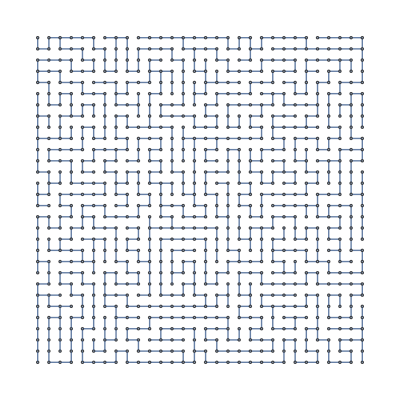
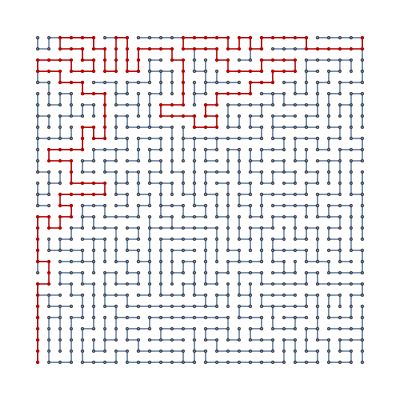

```mathematica
{ℱ,𝒢}={data["maze"],data["solved-maze"]}
```

Notice the purple border when you click the maze:

You can't analyze RandomMaze because its head is Graphics:

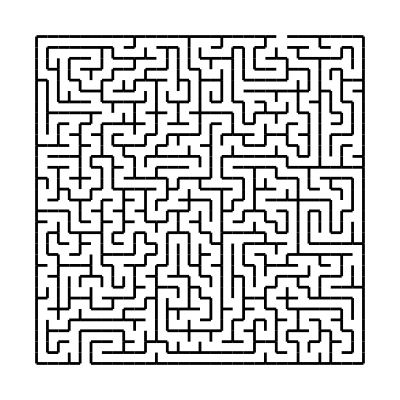

```mathematica
RandomMaze[30]
```

Notice the orange border, indicating Graphics:

```mathematica
Head[RandomMaze[30]]
```

Graphics

To analyze a maze encoded in Graphics you would have to use image processing, such as MorphologicalGraph.

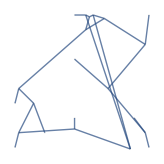

```mathematica
MorphologicalGraph[RandomMaze[10]]
```

This is similar from a documentation example for MorphologicalGraph:

Conversion of a maze into a graph:

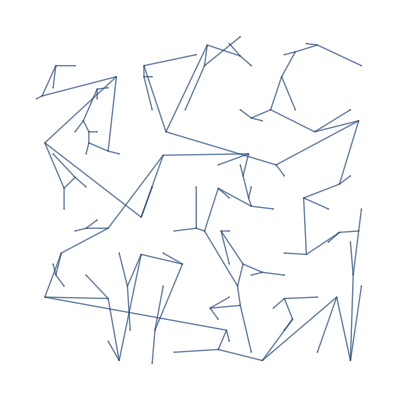

```mathematica
MorphologicalGraph[-Graphics-]
```

It matters if you use MorphologicalBinarse on the output from RandomMaze. MorphologicalGraph@MorphologicalBinarize[graph] and MorphologicalGraph@graph are not isomorphic.

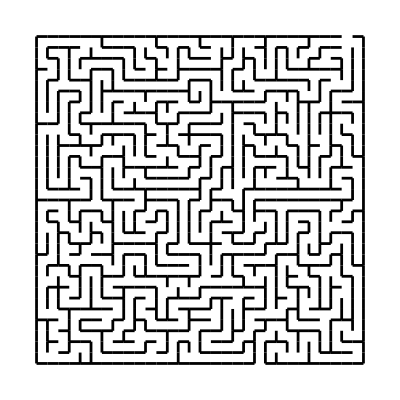

-Graphics-

```mathematica
MorphologicalBinarize[Echo@RandomMaze[30]]
```

```mathematica
graph=RandomMaze[30];
```

```mathematica
IsomorphicGraphQ[MorphologicalGraph@MorphologicalBinarize[graph],MorphologicalGraph@graph]
```

False

Here are some things you can analyze in the output maze, some more useful than others:

Adjacency matrix:

```mathematica
AdjacencyMatrix[𝒢]
```

SparseArray[…]

Color vertices:

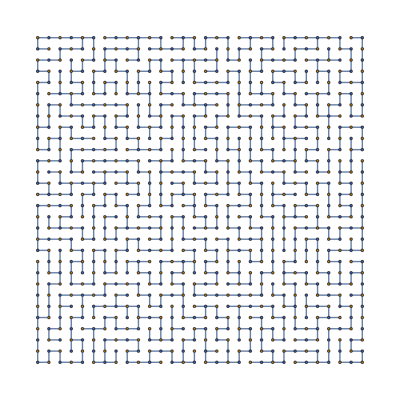

```mathematica
ResourceFunction["ColorGraphVertices"][ℱ]
```

Color edges:

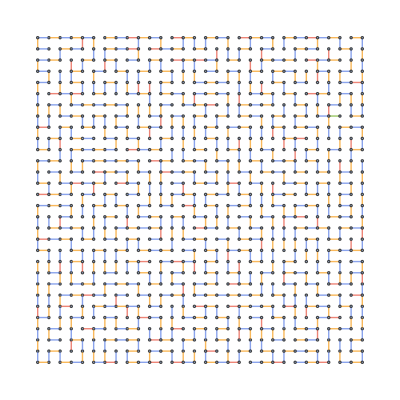

```mathematica
ResourceFunction["ColorGraphEdges"][ℱ]
```

Vertex chromatic number:

```mathematica
VertexChromaticNumber[ℱ]
```

2

Edge chromatic number

```mathematica
EdgeChromaticNumber[ℱ]
```

4

Chromatic polynomial:

```mathematica
Short[ChromaticPolynomial[data["maze"],x],3]
```

-x+899 x^2-403651 x^3+120691649 x^4-27034929376 x^5+«1335»+27034929376 x^896-120691649 x^897+403651 x^898-899 x^899+x^900

```mathematica
FullSimplify[ChromaticPolynomial[data["maze"],x]]//TraditionalForm
```

(x-1)^899 x

Vertex count:

```mathematica
VertexCount[ℱ]
```

900

Edge count:

```mathematica
EdgeCount[ℱ]
```

899

Vertex-degree:

```mathematica
ByteArray[VertexDegree[ℱ]]
```

ByteArray[…]

Highlight graph hubs, which have the greatest vertex degrees in the graph:

```mathematica
GraphHub[ℱ]
```

{803}

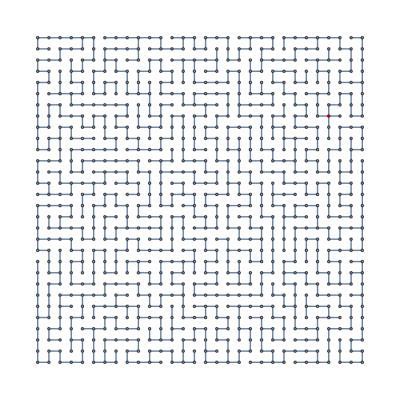

```mathematica
HighlightGraph[ℱ,GraphHub[ℱ]]
```

Highlight the start and end vertices:

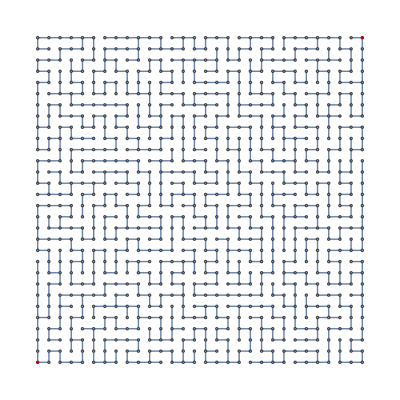

```mathematica
HighlightGraph[ℱ,{1,Last[VertexList[ℱ]]}]
```

Find the distance from the start to the end:

```mathematica
GraphDistance[ℱ,data["start"],data["end"]]
```

156

The data is already available:

```mathematica
data["distance"]
```

156

The mean graph distance:

```mathematica
MeanGraphDistance[data["maze"]]
```

33583466/202275

The distance matrix:

```mathematica
GraphDistanceMatrix[data["maze"]]
```

VertexEccentricity gives the length of the longest shortest path from the source s to every other vertex in the graph g.

```mathematica
VertexEccentricity[data["maze"],1]
```

350

```mathematica
VertexEccentricity[data["maze"],900]
```

262

GraphRadius gives the minimum eccentricity of the vertices in the graph g.

```mathematica
GraphRadius[data["maze"]]
```

228

Find the graph center, vertices with minimum eccentricity:

{658}

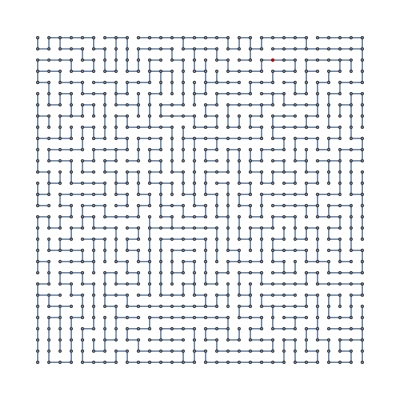

```mathematica
HighlightGraph[data["maze"],Echo@GraphCenter[data["maze"]]]
```

Notice that the graph center is on the solution path:

```mathematica
data["solved-maze"]
```

-Graphics-

```mathematica
data["shortest-path"]
```

{1,2,3,4,5,6,7,8,38,39,40,10,11,12,13,14,44,43,73,74,104,105,75,76,106,136,166,196,197,167,137,107,108,109,79,49,50,80,110,140,141,142,172,171,201,202,203,204,205,175,145,146,116,86,87,57,27,28,58,88,118,117,147,177,178,148,149,119,89,90,120,150,180,179,209,208,207,237,238,239,240,270,269,268,267,297,298,299,329,359,389,388,418,417,416,415,414,384,354,353,383,413,443,442,472,502,503,473,474,504,505,535,565,595,596,626,656,657,687,717,718,688,658,628,627,597,567,537,538,508,509,479,449,419,420,450,480,510,540,539,569,570,600,599,629,630,660,690,720,750,749,779,809,839,869,899,900}

```mathematica
SubsetQ[data["shortest-path"],GraphCenter[data["maze"]]]
```

True

GraphDiameter gives the greatest distance between any pair of vertices in the graph g.

```mathematica
GraphDiameter[data["maze"]]
```

456

GraphPeriphery gives vertices with maximum eccentricity:

{677,816}

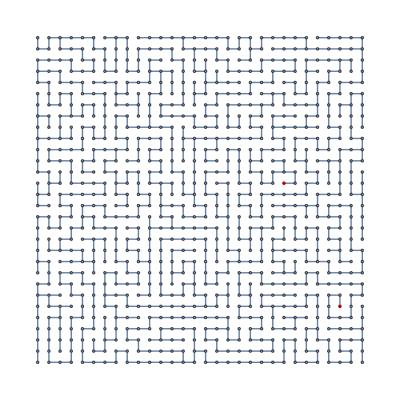

```mathematica
HighlightGraph[data["maze"],Echo@GraphPeriphery[data["maze"]]]
```

It seems like these are the farthest dead ends.

Find the number of vertices you need to delete to disconnect the graph:

```mathematica
VertexConnectivity[data["maze"]]
```

1

The edge connectivity of a graph g is the smallest number of edges whose deletion from g disconnects g.

```mathematica
EdgeConnectivity[data["maze"]]
```

1

GraphDensitypaclet:ref/GraphDensity is the ratio of the number of edges divided by the number of edges of a complete graph with the same number of vertices.

```mathematica
GraphDensity[data["maze"]]
```

1/450

Find how tightly connected a graph is compared to number of edges

```mathematica
GraphLinkEfficiency[data["maze"]]
```

148261759/181845225

```mathematica
ResourceFunction["ReadableForm"][N[GraphLinkEfficiency[data["maze"]]]]
```

0.8153184060785759

ClosenessCentralitypaclet:ref/ClosenessCentrality will give high centralities to vertices that are at a short average distance to every other reachable vertex

```mathematica
Short@ClosenessCentrality[data["maze"]]
```

{0.0056053,«898»,0.00797948}

BetweennessCentralitypaclet:ref/BetweennessCentrality will give high centralities to vertices that are on many shortest paths of other vertex pairs.

```mathematica
Short@BetweennessCentrality[data["maze"]]
```

{0.,898.,1794.,2688.,«893»,201120.,203123.,3580.}

Get a ShortestPathFunction for fast computation:

```mathematica
f=FindShortestPath[data["maze"],All,All]
```

ShortestPathFunction[{All,All},«»]

You could also do work with cycles and tours.

FindPostmanTourpaclet:ref/FindPostmanTour[g] 
finds a Chinese postman tour in the graph g of minimal length.

Find a tour that traverses every edge at least once:

```mathematica
Short@FindPostmanTour[data["maze"]]
```

{{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,«1786»,7<->6,6<->5,5<->4,4<->3,3<->2,2<->1}}

The maze is acyclic:

```mathematica
AcyclicGraphQ[data["maze"]]
```

True

There is only one set of edges that leads to the end:

```mathematica
FindEdgeIndependentPaths[data["maze"],data["start"],data["end"],Infinity]
```

{{1,2,3,4,5,6,7,8,38,39,40,10,11,12,13,14,44,43,73,74,104,105,75,76,106,136,166,196,197,167,137,107,108,109,79,49,50,80,110,140,141,142,172,171,201,202,203,204,205,175,145,146,116,86,87,57,27,28,58,88,118,117,147,177,178,148,149,119,89,90,120,150,180,179,209,208,207,237,238,239,240,270,269,268,267,297,298,299,329,359,389,388,418,417,416,415,414,384,354,353,383,413,443,442,472,502,503,473,474,504,505,535,565,595,596,626,656,657,687,717,718,688,658,628,627,597,567,537,538,508,509,479,449,419,420,450,480,510,540,539,569,570,600,599,629,630,660,690,720,750,749,779,809,839,869,899,900}}

```mathematica
Length[FindEdgeIndependentPaths[data["maze"],data["start"],data["end"],Infinity]]===1
```

True

There is only one set of vertices that leads to the end:

```mathematica
FindVertexIndependentPaths[data["maze"],data["start"],data["end"],Infinity]
```

{{1,2,3,4,5,6,7,8,38,39,40,10,11,12,13,14,44,43,73,74,104,105,75,76,106,136,166,196,197,167,137,107,108,109,79,49,50,80,110,140,141,142,172,171,201,202,203,204,205,175,145,146,116,86,87,57,27,28,58,88,118,117,147,177,178,148,149,119,89,90,120,150,180,179,209,208,207,237,238,239,240,270,269,268,267,297,298,299,329,359,389,388,418,417,416,415,414,384,354,353,383,413,443,442,472,502,503,473,474,504,505,535,565,595,596,626,656,657,687,717,718,688,658,628,627,597,567,537,538,508,509,479,449,419,420,450,480,510,540,539,569,570,600,599,629,630,660,690,720,750,749,779,809,839,869,899,900}}

```mathematica
Length[FindVertexIndependentPaths[data["maze"],data["start"],data["end"],Infinity]]===1
```

True

The shortest path graph is a subgraph:

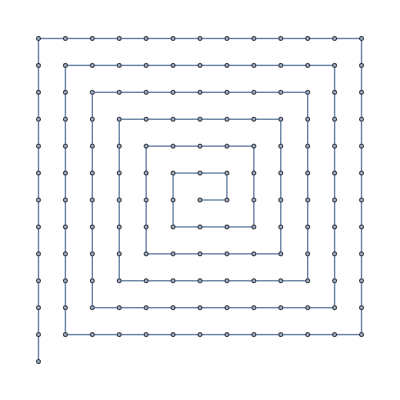

True

```mathematica
IsomorphicSubgraphQ[Echo@data["shortest-path-graph"],data["maze"]]
```

Find a subgraph isomorphism:

```mathematica
FindSubgraphIsomorphism[data["shortest-path-graph"],data["maze"]]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,38→38,39→39,40→40,10→10,11→11,12→12,13→13,14→14,44→44,43→43,73→73,74→74,104→104,105→105,75→75,76→76,106→106,136→136,166→166,196→196,197→197,167→167,137→137,107→107,108→108,109→109,79→79,49→49,50→50,80→80,110→110,140→140,141→141,142→142,172→172,171→171,201→201,202→202,203→203,204→204,205→205,175→175,145→145,146→146,116→116,86→86,87→87,57→57,27→27,28→28,58→58,88→88,118→118,117→117,147→147,177→177,178→178,148→148,149→149,119→119,89→89,90→90,120→120,150→150,180→180,179→179,209→209,208→208,207→207,237→237,238→238,239→239,240→240,270→270,269→269,268→268,267→267,297→297,298→298,299→299,329→329,359→359,389→389,388→388,418→418,417→417,416→416,415→415,414→414,384→384,354→354,353→353,383→383,413→413,443→443,442→442,472→472,502→502,503→503,473→473,474→474,504→504,505→505,535→535,565→565,595→595,596→596,626→626,656→656,657→657,687→687,717→717,718→718,688→688,658→658,628→628,627→627,597→597,567→567,537→537,538→538,508→508,509→509,479→479,449→449,419→419,420→420,450→450,480→480,510→510,540→540,539→539,569→569,570→570,600→600,599→599,629→629,630→630,660→660,690→690,720→720,750→750,749→749,779→779,809→809,839→839,869→869,899→899,900→898|>}

Find isomorphic subgraphs:

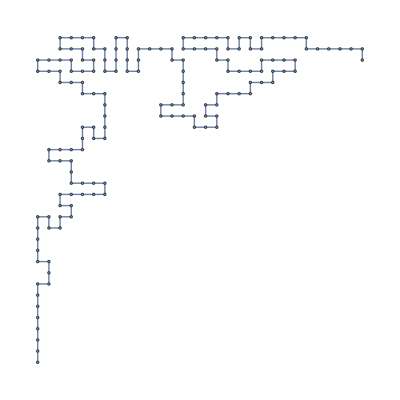

```mathematica
FindIsomorphicSubgraph[data["maze"],data["shortest-path-graph"]]
```

I will grant that RandomMaze does have nice Graphics. I might add an option for this. I tried looking at the source code for RandomMaze, but I couldn’t figure out a simple way to make Graphics.

Another advantage of this function compared to RandomGraph is you can generate rectangles and not just squares:

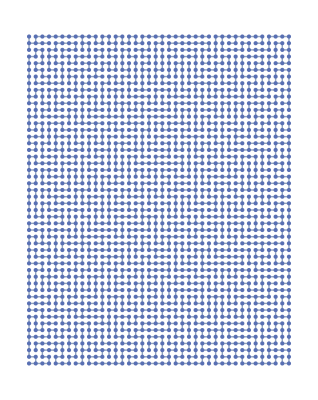
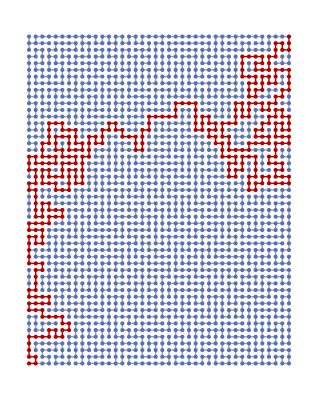
<|maze→-Graphics-,solved-maze→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{50,40}]
```

You can't do this with RandomMaze. You can do a 40 maze or a 50 maze but not both.

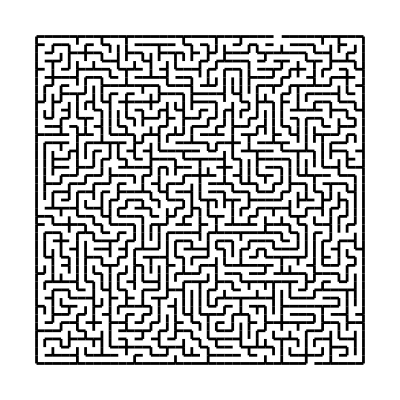

```mathematica
TimeConstrained[ResourceFunction["RandomMaze"][40],20]
```

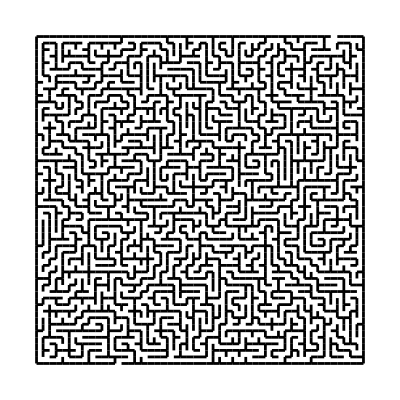

```mathematica
TimeConstrained[ResourceFunction["RandomMaze"][50],20]
```

Be sure to use delimiters between independent examples. I have added some below.

Find a solution to a random 20 by 30 maze:

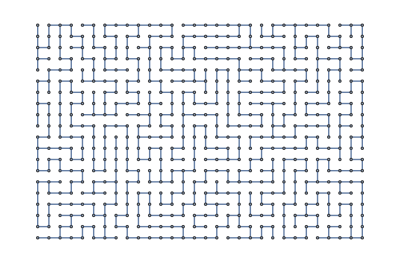
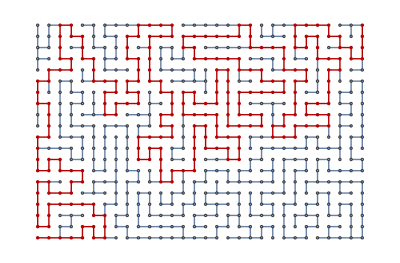
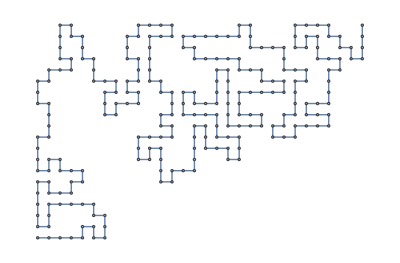
<|start→1,end→600,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→242,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomGridMazeSolution[{20,30}]
```

Find a solution to a random 50 by 60 maze:

```mathematica
FindRandomGridMazeSolution[{50,60}]
```

-Graphics-

Find a solution to a random 60 by 70 maze:

```mathematica
FindRandomGridMazeSolution[{60,70}]
```

-Graphics-

Solve a random 70 by 80 maze:

```mathematica
FindRandomGridMazeSolution[{70,80}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

mazes

graph algorithms

fun

### Categories

Cloud & Deployment
 External Interfaces & Connections
 Graphs & Networks
 Knowledge Representation & Natural Language
 Repository Tools
 Strings & Text
 User Interface Construction |  Core Language & Structure
 Financial Data & Computation
 Higher Mathematical Computation
 Machine Learning
 Scientific and Medical Data & Computation
 Symbolic & Numeric Computation
 Visualization & Graphics |  Data Manipulation & Analysis
 Geographic Data & Computation
 Images
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 System Operation & Setup
 Wolfram Physics Project |  Engineering Data & Computation
 Geometry
 Just For Fun
 Programming Utilities
 Sound & Video
 Time-Related Computation

### Related Symbols

FindShortestPath

### Related Resource Objects

RandomMaze

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.